```mathematica
sol=NDSolve[{v'[t]==x[t]-x[t]^3-0.05*v[t]+0.1 Cos[1.1*t],x'[t]==v[t],x[0]==0,v[0]==0},{x,v},{t,0,200},MaxSteps->3500];
```

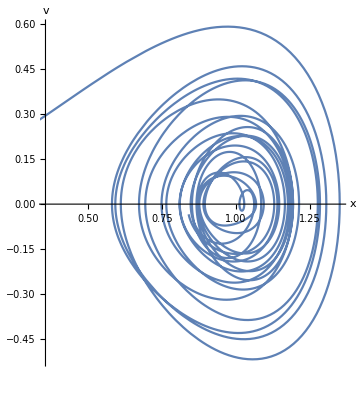

```mathematica
ParametricPlot[{x[t],v[t]}/. sol,{t,0,100},AxesLabel->{"x","v"}]
```

```mathematica
Clear[A];
solution[A_,tmax_]:=NDSolve[{v'[t]==x[t]-x[t]^3-0.05*v[t]+A*Cos[1.1*t],x'[t]==v[t],x[0]==0,v[0]==0},{x,v},{t,0,tmax},MaxSteps->100*tmax]
```

```mathematica
sol3=solution[0.2,800]
```

{{x→InterpolatingFunction[…],v→InterpolatingFunction[…]}}

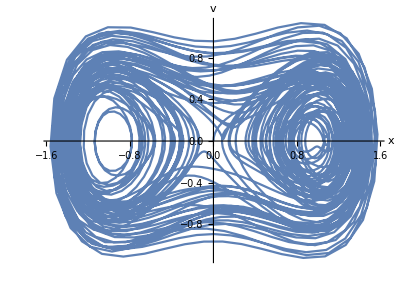

```mathematica
graph[tmin_,tmax_, sol_]:=ParametricPlot[Evaluate[{x[t],v[t]}/. sol],{t,tmin,tmax},AxesLabel->{"x","v"}]
graph[0,600,sol3]
```

The power spectra for these parameters looks  like chaotic

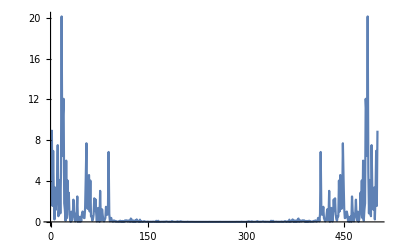

```mathematica
ListLinePlot[Abs[Fourier[Flatten[Table[Evaluate[x[t]/.sol3], {t,100,600}]]]]^2,PlotRange->All]
```

The complexity seems to come from the initial transient of the oscillator .

Lets plot for the latter times from 740 and 802:

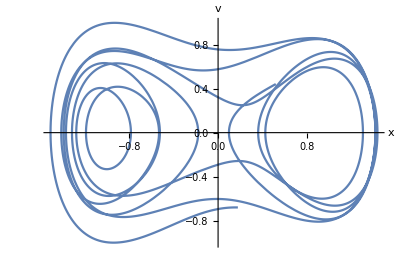

```mathematica
graph[740, 802, sol3]
```

{{x→InterpolatingFunction[…],v→InterpolatingFunction[…]}}

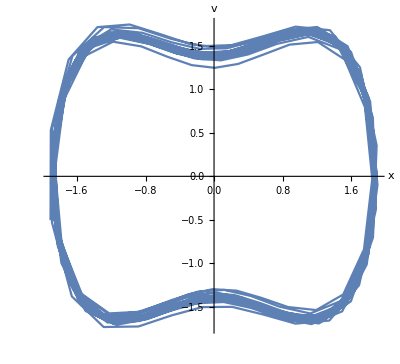

```mathematica
sol4 = solution[0.4,1000]
graph[100,800,sol4]
```

This section is about Poincare section . Rather than considering the phase space trajectory for all times . The Poincare section is just discrete set of phase space points of the particle at every period of the driving force at t = 2 π/ω, 3 π/ω,,,etc. For periodic orbit the Poincare section is single point, when the period is doubled it consists of two points and so on.

```mathematica
poincare[A_,γ_,ω_,ndrop_, nplot_,psize_]:= (T=2π/ω; g[{xold_,vold_}]:={x[T],v[T]} /. NDSolve[{v'[t]== x[t]-x[t]^3-γ*v[t]+A*Cos[ω t], x'[t]==v[t],x[0]==xold, v[0]==vold},{x,v},{t,0,T}][[1]];
lp=ListPlot[Drop[NestList[g,{0,0},nplot+ndrop],ndrop],PlotStyle->{PointSize[psize],Hue[0]},PlotRange->All,AxesLabel->{"x","v"}])
```

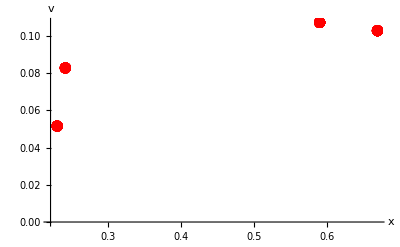

```mathematica
poincare[0.338,0.1, 1.4, 1900,100,0.02]
```

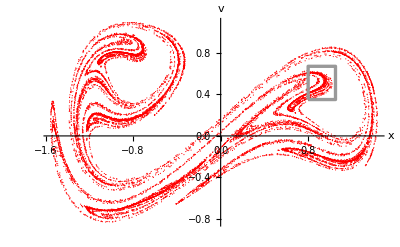

```mathematica
poincare[0.35,0.1,1.4,200,15000,0.002];
Show[lp, Epilog->{GrayLevel[0.6],Thickness[0.006],Line[{{0.8,0.35},{0.8,0.67},{1.05,0.67},{1.05,0.35},{0.8,0.35}}]}]
```

This is Duffing system with type of the driving force been composed of two  frequencies:

ẍ+2γ ẋ+ω^2 x + αx^3=S_1 sin(ν_1 t)+S_2 sin(ν_2 t)

```mathematica
motion = NDSolve[{x''[t]+1/10 x'[t]+x[t]+x[t]^3== Sin[5 t]+Sin[7 t],
x[0]==0, x'[0]==0}, x[t], {t,80,180}][[1]]
```

{x[t]→InterpolatingFunction[…][t]}

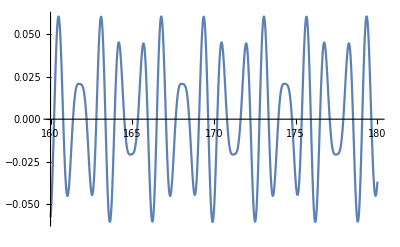

```mathematica
motionplt = Plot[x[t]/.motion, {t,160,180}, Ticks->False]
```

```mathematica
discretizedmotion = Table[x[t]/.motion, {t,80,180,.05}];
```

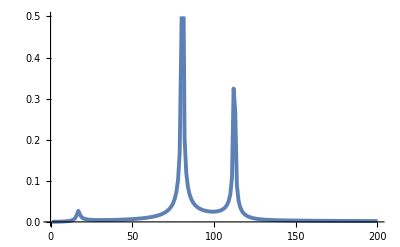

```mathematica
powerspectrum = ListPlot[Take[Abs[Fourier[discretizedmotion]],{1,200}], Joined->True,PlotRange->{0.,0.5}, PlotStyle->Thickness[0.007], Ticks->False]
```

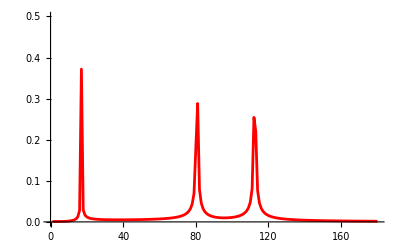

```mathematica
referencefreqs = Table[(Sin[t]+Sin[5t] + Sin[7t])/60,{t,100,200,0.05}];
referncesfreqplot = ListPlot[Take[Abs[Fourier[referencefreqs]],
{1,180}],Joined->True,PlotRange->{0,0.5},
PlotStyle->{Thickness[0.005],RGBColor[1,0,0]}, Ticks->False]
```

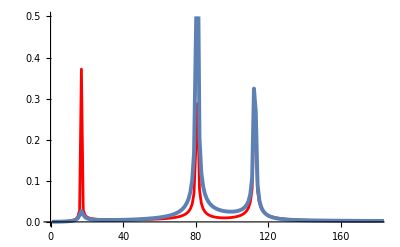

```mathematica
Show[{referncesfreqplot,powerspectrum}]
```

We see here the same power spectrum distribution as in the given oscillator. The ω = 1 is the frequency that should be transient.

```mathematica
motionω[n_]:= NDSolve[{x''[t]+1/10 x'[t]+n^2*x[t]+x[t]^3== Sin[5 t]+Sin[7 t],
x[0]==0, x'[0]==0}, x[t], {t,80,180}]
```

```mathematica
motion3ω =motionω[3]
```

{{x[t]→InterpolatingFunction[…][t]}}

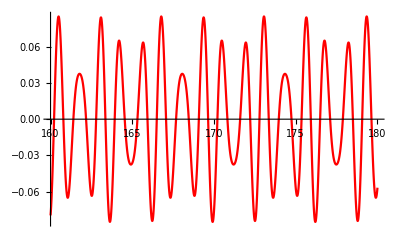

```mathematica
motion3plt = Plot[x[t]/.motion3ω, {t,160,180}, Ticks->False,PlotStyle->Red]
```

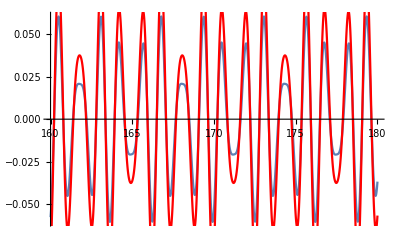

```mathematica
Show[{motionplt, motion3plt}]
```

```mathematica
motion15=motionω[15]
```

{{x[t]→InterpolatingFunction[…][t]}}

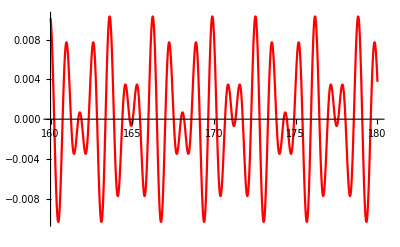

```mathematica
motion15plt = Plot[x[t]/.motion15, {t,160,180}, Ticks->False,PlotStyle->Red]
```

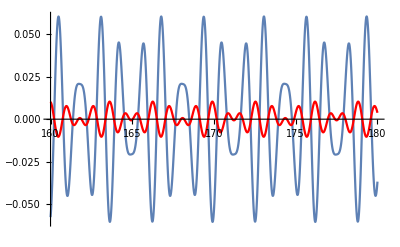

```mathematica
Show[{motionplt, motion15plt}]
```

```mathematica
motion19=motionω[19]
```

{{x[t]→InterpolatingFunction[…][t]}}

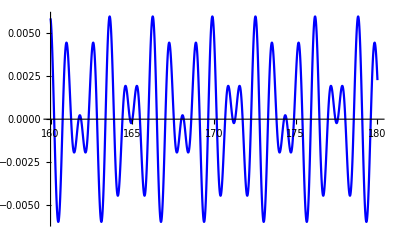

```mathematica
motion19plt = Plot[x[t]/.motion19, {t,160,180}, Ticks->False,PlotStyle->Blue]
```

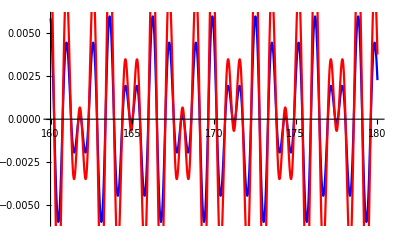

```mathematica
Show[{motion19plt, motion15plt}]
```